```mathematica
Manuel de la Cruz González 70909708H
```

```mathematica
ENTREGA 2.INTERPOLACIÓN Y APROXIMACIÓN DE FUNCIONES
```

```mathematica
EJERCICIO 2.1
```

```mathematica
datos=Import["C:\\Users\\Manu\\Desktop\\Programas Fortran\\Entrega 2\\datos.txt","Table"]
```

{{-10.,0.129776},{-9.,0.193452},{-8.,0.210419},{-7.,0.131653},{-6.,-0.0686905},{-5.,-0.362992},{-4.,-0.660285},{-3.,-0.833178},{-2.,-0.776776},{-1.,-0.469932},{0.,0},{1,0.469932},{2,0.776776},{3,0.833178},{4,0.660285},{5,0.362992},{6,0.0686905},{7,-0.131653},{8,-0.210419},{9,-0.193452},{10,-0.129776}}

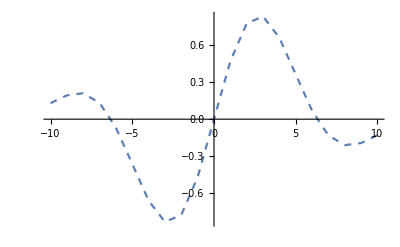

```mathematica
g=ListLinePlot[datos,PlotStyle->Dashed,PlotStyle->PointSize[0.03]]
```

```mathematica
datos2=Import["C:\\Users\\Manu\\Desktop\\Programas Fortran\\Entrega 2\\puntos.txt","Table"]
```

{{-10.,0.129776},{-9.8,0.143825},{-9.6,0.157619},{-9.4,0.17075},{-9.2,0.182825},{-9.,0.193452},{-8.8,0.202225},{-8.6,0.208728},{-8.4,0.212539},{-8.2,0.213238},{-8.,0.210419},{-7.8,0.203699},{-7.6,0.19273},{-7.4,0.177215},{-7.2,0.156912},{-7.,0.131653},{-6.8,0.101351},{-6.6,0.0660091},{-6.4,0.0257309},{-6.2,-0.0192753},{-6.,-0.0686905},{-5.8,-0.122084},{-5.6,-0.178913},{-5.4,-0.238525},{-5.2,-0.300168},{-5.,-0.362992},{-4.8,-0.426068},{-4.6,-0.488398},{-4.4,-0.548933},{-4.2,-0.606592},{-4.,-0.660285},{-3.8,-0.708932},{-3.6,-0.751487},{-3.4,-0.786966},{-3.2,-0.814463},{-3.,-0.833178},{-2.8,-0.842437},{-2.6,-0.841708},{-2.4,-0.830622},{-2.2,-0.808983},{-2.,-0.776776},{-1.8,-0.734177},{-1.6,-0.681552},{-1.4,-0.619453},{-1.2,-0.548613},{-1.,-0.469932},{-0.8,-0.384465},{-0.6,-0.2934},{-0.4,-0.198034},{-0.2,-0.0997535},{5.55112×10^-16,2.77555×10^-16},{0.2,0.0997535},{0.4,0.198034},{0.6,0.2934},{0.8,0.384465},{1.,0.469932},{1.2,0.548613},{1.4,0.619453},{1.6,0.681552},{1.8,0.734177},{2.,0.776776},{2.2,0.808983},{2.4,0.830622},{2.6,0.841708},{2.8,0.842437},{3.,0.833178},{3.2,0.814463},{3.4,0.786966},{3.6,0.751487},{3.8,0.708932},{4.,0.660285},{4.2,0.606592},{4.4,0.548933},{4.6,0.488398},{4.8,0.426068},{5.,0.362992},{5.2,0.300168},{5.4,0.238525},{5.6,0.178913},{5.8,0.122084},{6.,0.0686905},{6.2,0.0192753},{6.4,-0.0257309},{6.6,-0.0660091},{6.8,-0.101351},{7.,-0.131653},{7.2,-0.156912},{7.4,-0.177215},{7.6,-0.19273},{7.8,-0.203699},{8.,-0.210419},{8.2,-0.213238},{8.4,-0.212539},{8.6,-0.208728},{8.8,-0.202225},{9.,-0.193452},{9.2,-0.182825},{9.4,-0.17075},{9.6,-0.157619},{9.8,-0.143825},{10.,-0.129776}}

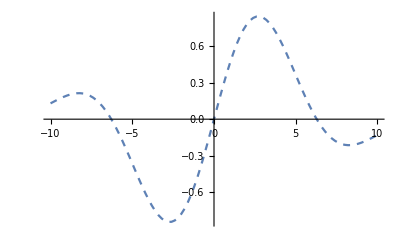

```mathematica
g2=ListLinePlot[datos2,PlotStyle->Dashed,PlotStyle->PointSize[0.03]]
```

```mathematica
Ejercicio 2.2
```

```mathematica
Tabla de datos inicial
```

```mathematica
datos3=Import["C:\\Users\\Manu\\Desktop\\Programas Fortran\\Entrega 2\\splines.txt","Table"]
```

{{72.33,319.},{82.33,325.},{99.,333.7},{104.3,339.7},{118.3,354.3},{128.3,356.3},{152.3,347.7},{166.3,341.7},{172.3,339.},{181.,339.7},{208.3,345.},{235.,346.3},{262.3,345.},{293.7,336.3},{328.7,322.3},{349.7,308.3},{356.3,303.7},{367.7,300.3},{384.3,298.3},{395.7,295.7},{403.,292.3}}

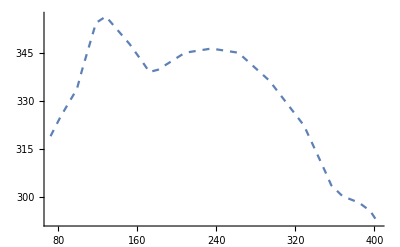

```mathematica
graf=ListLinePlot[datos3,PlotStyle->Dashed]
```

```mathematica
interpolacion=Import["C:\\Users\\Manu\\Desktop\\Programas Fortran\\Entrega 2\\interpolacion.txt","Table"]
```

{{72.33,319.},{75.6367,319.983},{78.9434,321.02},{82.2501,322.165},{85.5568,323.474},{88.8635,325.},{92.1702,326.765},{95.4769,328.66},{98.7836,330.542},{102.09,332.269},{105.397,333.7},{108.704,334.758},{112.01,335.631},{115.317,336.576},{118.624,337.847},{121.931,339.7},{125.237,342.291},{128.544,345.382},{131.851,348.638},{135.157,351.723},{138.464,354.3},{141.771,356.102},{145.077,357.132},{148.384,357.461},{151.691,357.16},{154.998,356.3},{158.304,354.965},{161.611,353.291},{164.918,351.423},{168.224,349.51},{171.531,347.7},{174.838,346.11},{178.144,344.743},{181.451,343.57},{184.758,342.565},{188.065,341.7},{191.371,340.951},{194.678,340.311},{197.985,339.775},{201.291,339.34},{204.598,339.},{207.905,338.761},{211.211,338.663},{214.518,338.754},{217.825,339.084},{221.132,339.7},{224.438,340.622},{227.745,341.746},{231.052,342.939},{234.358,344.068},{237.665,345.},{240.972,345.635},{244.278,346.011},{247.585,346.199},{250.892,346.272},{254.199,346.3},{257.505,346.33},{260.812,346.301},{264.119,346.127},{267.425,345.722},{270.732,345.},{274.039,343.896},{277.345,342.432},{280.652,340.649},{283.959,338.591},{287.266,336.3},{290.572,333.814},{293.879,331.155},{297.186,328.338},{300.492,325.381},{303.799,322.3},{307.106,319.133},{310.412,316.004},{313.719,313.059},{317.026,310.442},{320.333,308.3},{323.639,306.728},{326.946,305.629},{330.253,304.856},{333.559,304.262},{336.866,303.7},{340.173,303.056},{343.479,302.345},{346.786,301.617},{350.093,300.919},{353.4,300.3},{356.706,299.795},{360.013,299.379},{363.32,299.017},{366.626,298.669},{369.933,298.3},{373.24,297.878},{376.546,297.402},{379.853,296.876},{383.16,296.307},{386.467,295.7},{389.773,295.06},{393.08,294.393},{396.387,293.706},{399.693,293.006}}

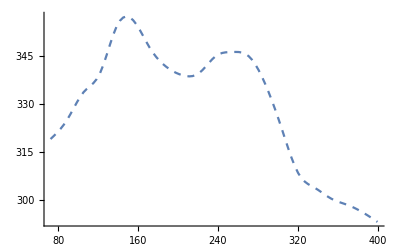

```mathematica
grafinter=ListLinePlot[interpolacion,PlotStyle->Dashed]
```

Funcion interpoladora en Mathematica

```mathematica
pnts=Import["C:\\Users\\Manu\\Desktop\\Programas Fortran\\Entrega 2\\splines.txt","Table"]
```

{{72.33,319.},{82.33,325.},{99.,333.7},{104.3,339.7},{118.3,354.3},{128.3,356.3},{152.3,347.7},{166.3,341.7},{172.3,339.},{181.,339.7},{208.3,345.},{235.,346.3},{262.3,345.},{293.7,336.3},{328.7,322.3},{349.7,308.3},{356.3,303.7},{367.7,300.3},{384.3,298.3},{395.7,295.7},{403.,292.3}}

```mathematica
Needs["Splines`"]
```

```mathematica
spline=SplineFit[pnts,Cubic]
```

SplineFunction[Cubic, {0.,20.}, <>]

20

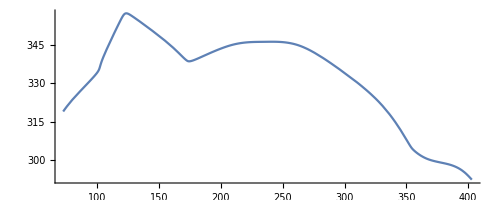

ParametricPlot::plln: Limiting value n in {u, 0, n} is not a machine-sized real number.

```mathematica
Needs["Splines`"]
spline=SplineFit[pnts,Cubic]
n=20
g=ParametricPlot[spline[u],{u,0,n}]
```